CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Thu 1 Jan 2026. Please

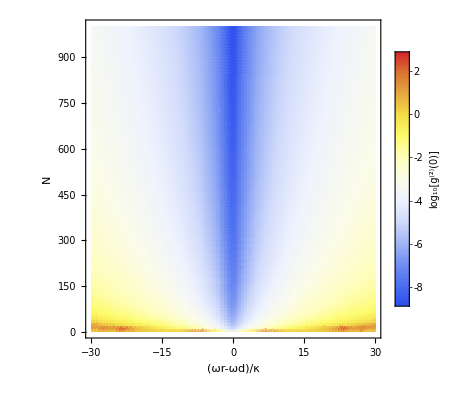

```mathematica
Clear["Global`*"];
LaunchKernels[300];

data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;


g=0.01*ωr;
γ=0.1*g;
κ=0.1*g;
E1=3*κ;


max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=100;
max2=1001;
min2=1;
segment2=100;
Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=IntegerPart[max2-(max2-min2)*((s-1)/segment2)];
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));
ωqdeviation=10^-3*ωq;
deltadata=RandomReal[NormalDistribution[ωq,ωqdeviation],Na]-ωq;
equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,g*√2*(Sum[ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,g*(Sum[ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])*√6+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,Na,logg20},{m,1,100+1,1},{s,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


data3Dflatten=Flatten[data,1];
ListDensityPlot[data3Dflatten,FrameLabel->{"(ωr-ωd)/κ","N"},ColorFunction->"TemperatureMap",BaseStyle->{FontSize->16,FontFamily->"Calibri"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```

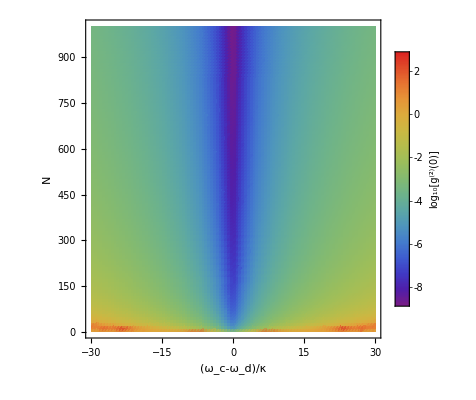

```mathematica
ListDensityPlot[data3Dflatten,FrameLabel->{"(ω_c-ω_d)/κ","N"},ColorFunction->"Rainbow",BaseStyle->{FontSize->16,FontFamily->"Calibri"},AxesOrigin->{-30,1000}, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```

```mathematica
Export["/home/u000011703749/fig2a.eps",-Graphics-]
```

/home/u000011703749/fig2a.eps

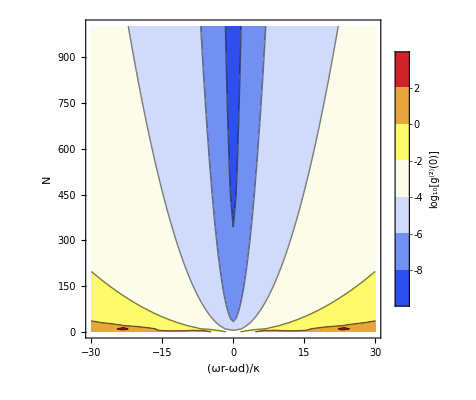

```mathematica
ListContourPlot[data3Dflatten,FrameLabel->{"(ωr-ωd)/κ","N"},ColorFunction->"TemperatureMap",BaseStyle->{FontSize->16,FontFamily->"Calibri"},AxesOrigin->{-30,1000}, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```

```mathematica
threeD2JC=Export["/home/u000011703749/3D2JC.txt",data3Dflatten,"Table"]
```

/home/u000011703749/3D2JC.txt

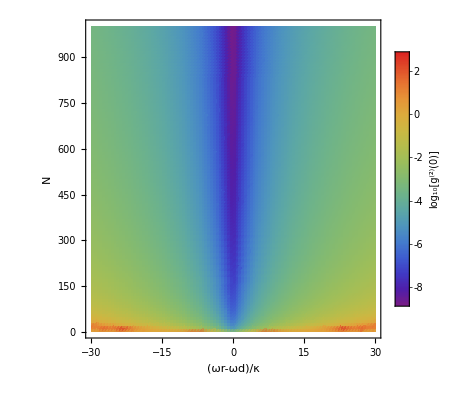

```mathematica
data3Dflatten=Import["/home/u000011703749/3D2JC.txt","Table"];
ListDensityPlot[data3Dflatten,FrameLabel->{"(ωr-ωd)/κ","N"},ColorFunction->"Rainbow",BaseStyle->{FontSize->16,FontFamily->"Calibri"},AxesOrigin->{-30,1000}, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```